{}

{{23}→{1,23},{1}→{1,23},{54}→{3,54},{3}→{3,54},{7}→{7,19},{19}→{7,19},{21}→{4,21},{4}→{4,21},{2}→{1,2,23},{1,23}→{1,2,23},{3,54}→{3,7,19,54},{7,19}→{3,7,19,54},{4,21}→{1,2,4,21,23},{1,2,23}→{1,2,4,21,23},{3,7,19,54}→{1,2,3,4,7,19,21,23,54},{1,2,4,21,23}→{1,2,3,4,7,19,21,23,54}}

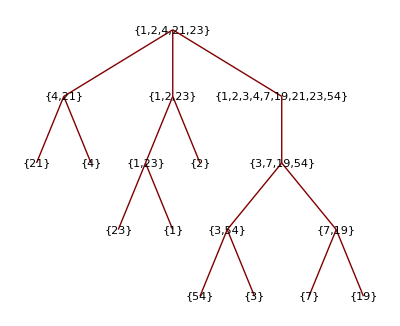

{{23},{1},{54},{3},{7},{19},{21},{4},{2},{1,23},{3,54},{7,19},{4,21},{1,2,23},{3,7,19,54},{1,2,4,21,23},{1,2,3,4,7,19,21,23,54}}

```mathematica
toBeSorted = {{23},{1},{54},{3},{7},{19},{21},{4},{2}};
listLength = Length[toBeSorted];
i=1;
mergeTree = {};
newNodeSet ={}
While[Length[toBeSorted[[Length[toBeSorted]]]]≠listLength,
If[i== Length[toBeSorted],
newNodeSet = newNodeSet ~Join~ toBeSorted[[i]];
toBeSorted = newNodeSet;
newNodeSet={};
i=1
,
If[i> Length[toBeSorted],
toBeSorted=newNodeSet;
i=1
,
newNode = Sort[toBeSorted[[i]] ~ Join ~ toBeSorted[[i+1]]];
mergeTree = mergeTree ~Join~ {toBeSorted[[i]] -> newNode,toBeSorted[[i+1]] -> newNode};
toBeSorted = Append[toBeSorted,newNode];
i+= 2;
]
];

]
mergeTree
TreePlot[mergeTree, VertexLabeling->True]
toBeSorted
```